Solution 1

#### Solve ẋ=a+noise. ṗ=-a(∂p)/(∂x) +q/2(∂^2 p)/(∂x^2)

Define pde

```mathematica
pde=D[p[x,t],t]== -a D[p[x,t],x]+q/2*D[p[x,t],x,x]
```

p^(0,1)[x,t]==-a p^(1,0)[x,t]+1/2 q p^(2,0)[x,t]

Solve PDE without noise for generic initial condition function

```mathematica
soln=DSolve[{D[p[x,t],t]== -a D[p[x,t],x],p[x,0]==p0[x]},p[x,t],{x,t}]
```

{{p[x,t]→p0[-a t+x]}}

Solve initial value problem gausiian PDE

```mathematica
sol=Simplify[DSolve[{pde,p[x,0]==Exp[-(x-x0)^2/2/s2]/Sqrt[2*Pi*s2]},p[x,t],{x,t}],{s2>0}]
```

{{p[x,t]→(ⅇ^(-(a t-x+x0)^2/(2 (s2+q t))))/(√(2 π) √(s2+q t))}}

Check that it is a probability distribution

```mathematica
Simplify[Integrate[p[x,t]/.sol,{x,-Infinity,Infinity}],{q>0,t>0,s2>0}]
```

{1}

Compute the mean value

```mathematica
Simplify[Integrate[x*p[x,t]/.sol,{x,-Infinity,Infinity}],{q>0,t>0,s2>0}]
```

{a t+x0}

Compute the covariance

```mathematica
Simplify[Integrate[x^2*p[x,t]/.sol,{x,-Infinity,Infinity}],{q>0,t>0,s2>0}]-(Simplify[Integrate[x*p[x,t]/.sol,{x,-Infinity,Infinity}],{q>0,t>0,s2>0}])^2
```

{s2+q t}

```mathematica
Plot3D[(p[x,t]/.sol)/.{a-> 0.2,q-> 1},{x,-4,4},{t,0,4}]
```

-Graphics3D-

#### Check the use of green’s functions

```mathematica
f0[x_]= 1/(√(2*σ*Pi))Exp[-(x-x0)^2/(2*σ)]
```

(ⅇ^(-(x-x0)^2/(2 σ)))/(√(2 π) √σ)

```mathematica
Simplify[1/(√(2*q*t*Pi))Integrate[f0[y]*Exp[-(x-y)^2/(2*q*t)],{y,-Infinity,Infinity}],{q>0,t>0,σ>0}]
```

(ⅇ^(-(x-x0)^2/(2 (q t+σ))))/(√(2 π) √(q t+σ))

Solution 2

#### Solve ẋ=a x+noise. ṗ=-a x(∂p)/(∂x) -p a+q/2(∂^2 p)/(∂x^2)

Solve the ODE

ⅇ^(a t) x0

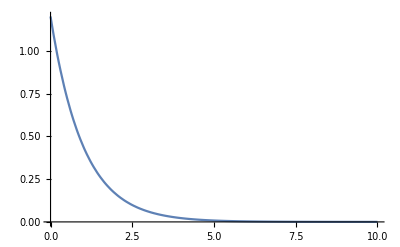

```mathematica
solODE = DSolve[{x'[t]==a*x[t],x[0]==x0},x[t],t]⟦1,1,2⟧
Plot[solODE/.{a->-1,x0-> 1.2},{t,0,10}, PlotRange->Full]
```

Solve pde without noise

```mathematica
pdeXnonoise=D[p[x,t],t]== -a*x*D[p[x,t],x] - p[x,t]*a
```

p^(0,1)[x,t]==-a p[x,t]-a x p^(1,0)[x,t]

```mathematica
sol = DSolve[{pdeXnonoise,p[x,0]==p0[x]},p[x,t],{x,t}]
```

{{p[x,t]→ⅇ^(-a t) p0[ⅇ^(-a t) x]}}

```mathematica
sol=DSolve[{pdeXnonoise,p[x,0]==Exp[-(x-x0)^2/2/s2]/Sqrt[2*Pi*s2]},p[x,t],{x,t}]
```

{{p[x,t]→(ⅇ^(-a t-((ⅇ^(-a t) x-x0)^2)/(2 s2)))/(√(2 π) √s2)}}

```mathematica
Plot3D[(p[x,t]/.sol)/.{a-> -1,q-> 1,x0->1,s2->0.2},{x,-4,10},{t,0,4},PlotRange->Full]
```

-Graphics3D-

Solve with noise

```mathematica
pdeX=D[p[x,t],t]== -a*x*D[p[x,t],x] - p[x,t]*a+q/2*D[p[x,t],x,x]
sol=DSolve[{pdeX,p[x,0]==Exp[-(x-x0)^2/2/s2]/Sqrt[2*Pi*s2]},p[x,t],x,t]
sol=NDSolve[{pdeX,p[-10,t]==0,p[10,t]==0,p[x,0]==Exp[-(x-x0)^2/2/s2]/Sqrt[2*Pi*s2]}/.{a-> -1,q-> 0.3,x0->1,s2->0.1},p[x,t],{x,-10,10},{t,0,10}]
```

p^(0,1)[x,t]==-a p[x,t]-a x p^(1,0)[x,t]+1/2 q p^(2,0)[x,t]

DSolve[{p^(0,1)[x,t]==-a p[x,t]-a x p^(1,0)[x,t]+1/2 q p^(2,0)[x,t],p[x,0]==(ⅇ^(-(x-x0)^2/(2 s2)))/(√(2 π) √s2)},p[x,t],x,t]

{{p[x,t]→InterpolatingFunction[{{-10., 10.}, {0., 10.}}, <>][x,t]}}

```mathematica
Plot3D[(p[x,t]/.sol),{x,-Pi,1.5Pi},{t,0,5},PlotRange->Full]
```

-Graphics3D-

Solution 3

#### Solve ẋ=a Sin x+noise. ṗ=-a x(∂p)/(∂x) -p a+q/2(∂^2 p)/(∂x^2)

Solve PDE without noise for generic initial condition function

```mathematica
pdeNonoise = D[p[x,t],t]== -a*Sin[x]*D[p[x,t],x] - p[x,t]*a*Cos[x]
```

p^(0,1)[x,t]==-a Cos[x] p[x,t]-a Sin[x] p^(1,0)[x,t]

```mathematica
soln=DSolve[{pdeNonoise,p[x,0]==p0[x]},p[x,t],{x,t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p[x,t]→Csc[x] p0[2 ArcCot[ⅇ^(a t) Cot[x/2]]] Sin[2 ArcCot[ⅇ^(a t) Cot[x/2]]]}}

```mathematica
pde2=D[p[x,t],t]== -a*Sin[x]*D[p[x,t],x] - p[x,t]*a*Cos[x]+q/2*D[p[x,t],x,x]
```

p^(0,1)[x,t]==-a Cos[x] p[x,t]-a Sin[x] p^(1,0)[x,t]+1/2 q p^(2,0)[x,t]

```mathematica
sol=NDSolve[{pde2,p[-10,t]==0,p[10,t]==0,p[x,0]==Exp[-(x-x0)^2/2/s2]/Sqrt[2*Pi*s2]}/.{a-> 1,q-> 0.4,x0->1,s2->0.2},p[x,t],{x,-10,10},{t,0,10}]
```

{{p[x,t]→InterpolatingFunction[{{-10., 10.}, {0., 10.}}, <>][x,t]}}

```mathematica
Plot3D[p[x,t]/.sol,{x,-Pi,1.5Pi},{t,0,10},PlotRange->Full]
```

-Graphics3D-

```mathematica
pde2=D[p[x1,x2,t],t]== -x2*D[p[x1,x2,t],x1]+a*x1*D[p[x1,x2,t],x2]
```

#### Solve the ODE

```mathematica
solODE = DSolve[{x'[t]==a*Sin[x[t]],x[0]==x0},x[t],t]⟦1,1,2⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2 ArcCot[ⅇ^(-a t) Cot[x0/2]]

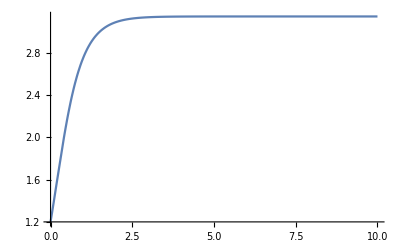

```mathematica
Plot[solODE/.{a->2,x0-> 1.2},{t,0,10}, PlotRange->Full]
```

```mathematica
solODE = NDSolve[{x''[t]==-2*Sin[x[t]],x[0]==1,x'[0]==0},{x[t],x'[t]},{t,0,2*Pi}]
```

{{x[t]→InterpolatingFunction[{{0., 6.28319}}, <>][t],x'[t]→InterpolatingFunction[{{0., 6.28319}}, <>][t]}}

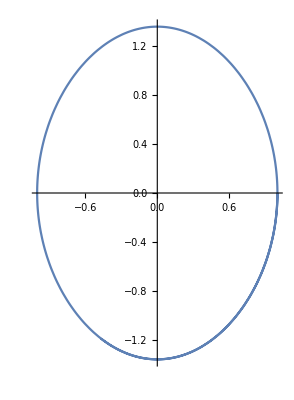

```mathematica
ParametricPlot[{x[t]/.solODE[[1,1]],x'[t]/.solODE[[1,2]]},{t,0,2*Pi}]
```

sol2

```mathematica
pde2=D[p[x,t],t]== -a*D[p[x,t],x] - p[x,t]*a +q/2*D[p[x,t],x,x]
sol=DSolve[{pde2,p[x,0]==Exp[-(x-x0)^2/2/s2]/Sqrt[2*Pi*s2]},p[x,t],{x,t}]
```

p^(0,1)[x,t]==-a p[x,t]-a p^(1,0)[x,t]+1/2 q p^(2,0)[x,t]

{{p[x,t]→(ⅇ^(-a t-(a t-x+x0)^2/(2 (s2+q t))) √(1/s2) √s2)/(√(2 π) √(s2+q t))}}

Solution 1.b

#### Solve ẋ=a+noise. ṗ=-a(∂p)/(∂x) +q/2(∂^2 p)/(∂x^2) where x∈ℝ^2

```mathematica
pde=D[p[x,y,t],t]== -ax D[p[x,y,t],x]-ax D[p[x,y,t],y]+qxx/2*D[p[x,y,t],x,x]+qxy*D[p[x,y,t],x,y]+qyy/2*D[p[x,y,t],y,y] /. {ax-> 2,ay-> 3,qxx-> 0.1, qxy-> 0.01, qyy-> 0.2}
```

p^(0,0,1)[x,y,t]==-2 p^(0,1,0)[x,y,t]+0.1 p^(0,2,0)[x,y,t]-2 p^(1,0,0)[x,y,t]+0.01 p^(1,1,0)[x,y,t]+0.05 p^(2,0,0)[x,y,t]

```mathematica
icond = p[x,y,0]==Exp[-(x-x0)^2/2/s2]/Sqrt[2*Pi*s2]*Exp[-(y-y0)^2/2/s2]/Sqrt[2*Pi*s2] /.{x0->3,y0-> 2,s2->0.5}
```

p[x,y,0]==0.31831 ⅇ^(-1. (-3+x)^2-1. (-2+y)^2)

```mathematica
sol=Simplify[NDSolve[{pde,icond},p[x,y,t],{x,y,t}],{s2>0}]
```

NDSolve::underdet: There are more dependent variables, {p[x,y,0],p[x,y,t],p^(0,0,1)[x,y,t],p^(0,1,0)[x,y,t],p^(0,2,0)[x,y,t]}, than equations, so the system is underdetermined.

NDSolve[{p^(0,0,1)[x,y,t]+2 (p^(0,1,0)[x,y,t]+p^(1,0,0)[x,y,t])==0.1 p^(0,2,0)[x,y,t]+0.01 p^(1,1,0)[x,y,t]+0.05 p^(2,0,0)[x,y,t],p[x,y,0]==0.31831 ⅇ^(-1. (-3.+x)^2-1. (-2.+y)^2)},p[x,y,t],{x,y,t}]

```mathematica
pde=D[p[x,y,t],t]== -a1*D[p[x,y,t],x]-a2*D[p[x,y,t],y]
```

p^(0,0,1)[x,y,t]==-a2 p^(0,1,0)[x,y,t]-a1 p^(1,0,0)[x,y,t]

```mathematica
sol=Simplify[DSolve[{pde,p[x,y,0]==F[x,y,0]},p[x,y,t],{x,y,t}],{s2>0}]
```

```mathematica
DSolve[{Derivative[0,0,1][p][x,y,t]+a2 Derivative[0,1,0][p][x,y,t]+a1 Derivative[1,0,0][p][x,y,t]==0,F[x,y,0]==p[x,y,0]},p[x,y,t],{x,y,t}]
```

DSolve[{p^(0,0,1)[x,y,t]+a2 p^(0,1,0)[x,y,t]+a1 p^(1,0,0)[x,y,t]==0,F[x,y,0]==p[x,y,0]},p[x,y,t],{x,y,t}]

Solution 3

#### Solve ẍ=-a sin x + noise